```mathematica
并联耦合摆的能谱计算
```

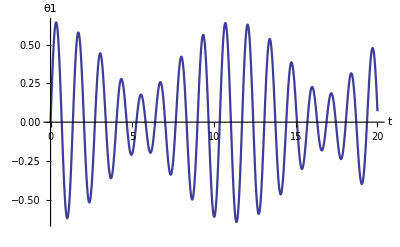

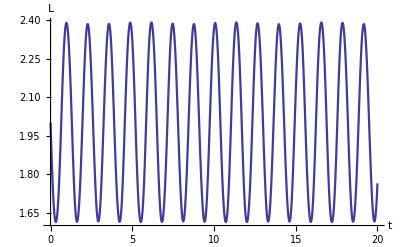

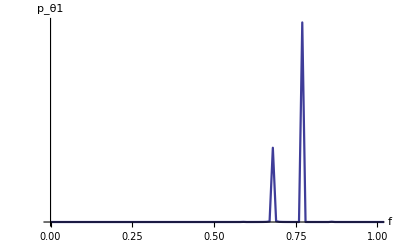

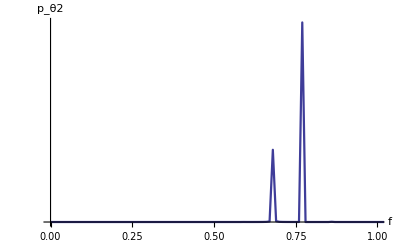

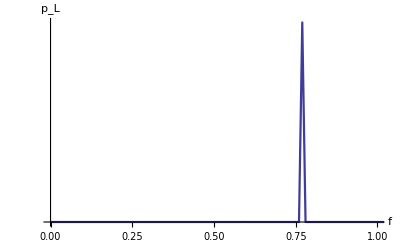

```mathematica
g=9.8;m1=0.2;m2=0.2;tm=100.0;
width=2;L1=0.5;k=0.5;
initial1={0,1.5/L1};initial2={0,-0.5/L1};
P1=(width-L1 (Sin[θ1[t]]-Sin[θ2[t]]))^2;
P2=L1^2 (Cos[θ1[t]]-Cos[θ2[t]])^2;
L=√(P1+P2);
equ={θ1''[t]==
(width/L1 Cos[θ1[t]]+Sin[θ2[t]-θ1[t]]) k/m1 
*(1-width/L)-g/L1 Sin[θ1[t]],
θ2''[t]==
-(width/L1 Cos[θ2[t]]+Sin[θ2[t]-θ1[t]]) k/m2 
*(1-width/L)-g/L1 Sin[θ2[t]],
θ1[0]==initial1[[1]],θ1'[0]==initial1[[2]],θ2[0]==initial2[[1]],θ2'[0]==initial2[[2]]};
s=NDSolve[equ,{θ1,θ2},{t,0,tm},MaxSteps->∞];
{θ1,θ2}={θ1,θ2}/.s[[1]];

Plot[θ1[t],{t,0,tm/5},PlotPoints->100,
AxesLabel->{"t","θ1"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],
BaseStyle->{FontSize->13}]
Plot[L,{t,0,tm/5},PlotPoints->100,
AxesLabel->{"t","L"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],
BaseStyle->{FontSize->13}]

sample=2000;
signal=Table[θ1[t],{t,0,tm,tm/sample}];
fs=Fourier[signal];ps=Abs[fs]^2;
len=Length[fs];
fs=Table[{(j-1)/tm,fs[[j]]},{j,len}];
ps=Table[{(j-1)/tm,ps[[j]]},{j,len}];
ListLinePlot[ps,PlotRange->{{0,1},All},
Ticks->{Automatic,None},
AxesLabel->{"f","p_θ1"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],
BaseStyle->{FontSize->13}]

signal=Table[θ2[t],{t,0,tm,tm/sample}];
fs=Fourier[signal];ps=Abs[fs]^2;
len=Length[fs];
fs=Table[{(j-1)/tm,fs[[j]]},{j,len}];
ps=Table[{(j-1)/tm,ps[[j]]},{j,len}];
ListLinePlot[ps,PlotRange->{{0,1},All},
Ticks->{Automatic,None},
AxesLabel->{"f","p_θ2"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],
BaseStyle->{FontSize->13}]

av=Sum[L,{t,0.,tm,tm/sample}]/sample;
signal=Table[(L-av),{t,0.,tm,tm/sample}];
fs=Fourier[signal];ps=Abs[fs]^2;
len=Length[fs];
fs=Table[{(j-1)/tm,fs[[j]]},{j,len}];
ps=Table[{(j-1)/tm,ps[[j]]},{j,len}];
ListLinePlot[ps,PlotRange->{{0,1},All},
Ticks->{Automatic,None},
AxesLabel->{"f","p_L"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003],
BaseStyle->{FontSize->13}]

Clear[equ,θ1,θ2,signal,ps,fs]
```